# Mathematica: The Doorway to your Dreams

The power of programming is that once you understand the syntax for a simple computation, it is trivial to extend the code to do an incredibly complex task.

## Before we Begin

#### Explore: Dynamic Functionality

Start exploring this notebook on your own. All you need is a mouse! Play around with the sliders and other controllers below and see what happens

```mathematica
(* Rotating about a point *)
Manipulate[Graphics[{Gray,Rectangle[],Black,Rotate[Rectangle[],θ,center],Red,PointSize[0.03],Point[center]}, PlotRange->2, Axes->True],
"The rotation variable runs from 0 to 2π:",
{θ,0,2π, ControlType -> Animator, ImageSize -> Small},
Delimiter,
"Rotation happens around whatever center the user specifies",
{{center,{0,0}},{0,0},{1,1}, ControlType -> Slider2D},
ControlPlacement -> Left
]
```

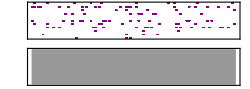

```mathematica
(* Random music *)
Sound[Table[SoundNote[NestList[#+4&,-24,n=10](RandomChoice[{1-#,#}->{0,1}]&/@(RealDigits[N[1/7,n+1]][[1]]/50))/.x_/;x==0->None,0.25],{102}]]
```

```mathematica
(* Pretty graphic *)
Manipulate[Graphics[Polygon[Table[r^n{-Sin[n*a],Cos[n*a]},{n,0,L}]],PlotRange->P],
{P,1,0},{{r,.98},1,.95},{{a,2.6},0,2Pi}, {{L,300},1,1000,1}]
```

```mathematica
(* Bouncing balls *)
Framed@DynamicModule[{contents={}},EventHandler[Graphics[{PointSize[0.1],Point[Dynamic[contents=Map[If[#[[1,2]]≥0,{#[[1]]-#[[2]],#[[2]]+{0,0.001}},{{#[[1,1]],0},{1,-(0.8+RandomReal[{0,0.2}])}#[[2]]}]&,contents];Map[First,contents]]]},PlotRange->{{0,1},{0,1}}],"MouseDown":>(AppendTo[contents,{MousePosition["Graphics"],{0,0}}])]]
```

```mathematica
(* Pottery *)
DynamicModule[{dd=3Pi/2,f,pts={{0,2},{1,2},{3,3},{5,2},{6,2},{7,3},{9,3}}},
f=Interpolation[pts,InterpolationOrder->2,Method->"Spline"];
Grid[{
{LocatorPane[Dynamic[pts,(f=Interpolation[#,InterpolationOrder->2,Method->"Spline"];pts=#)&],Dynamic[Plot[f[t],{t,0,9},PlotRange->{{0,9},{0,4}}]]],
Slider[Dynamic[dd],{.1,2Pi}]},
{Dynamic[RevolutionPlot3D[{f[t]},{t,0,9},{d,0,dd},Mesh->None,PlotStyle->Directive[Orange,Specularity[White,10]],RevolutionAxis->{1,0,0},PlotRange->{All,{-4,4},{-4,4}},ImageSize->500],TrackedSymbols:>{f,dd}],SpanFromLeft}
}]
]
```

## Beginner Section: A Gentle-ish Introduction

Open/close sections by mouse clicking on them.
Important sections are marked with (!!!)

### Basics

#### A Fancy Calculator

The journey of a thousand miles, starts with a single step. Let’s do some addition and multiplication.
Evaluate these commands using Shift + Enter (or NumPad Enter if you have one)

```mathematica
1+1
```

```mathematica
(-2)*(-2)
```

Evaluate 15/48+19/400+16/25

What is the last digit of 2^1000

#### The Rules

The rules for the Mathematica language are:

Built-in commands begin with a capital letter and are non-abbreviated, standard English words. Ex: , , ...

Exception class 1: Mathematical shorthand notations (, , , , )

Exception class 2: Numerical functions involving  (which stands for numerical) such as in  or  (which numerically solve a system of equations or numerically integrate)

Symbols defined by the user should begin with lowercase letters but can include letters and numbers

#### (!!!) Brackets

Braces {} enclose lists. Create a list with the elements 1, 5, 25, 125, 625, 3125, 15625, and 78125

Brackets [] enclose arguments in functions. Apply the function Exp (the exponential function) of the arguments 5, 0, and x. These yield the values ⅇ^5, ⅇ^0=1, and ⅇ^x, respectively

Parentheses () are used exclusively for grouping. Normal order of operations would evaluate 2*3+4 as (2*3)+4=10. If we instead want to evaluate 2*(3+4)=14 we must add parentheses

#### Explore: Table, Sum

The  function is useful for constructing lists. Create a list of the first 10  numbers. Then create a list of the first 1000 prime numbers.

The function  evaluates a sum of terms (it allows symbolic bounds!). Evaluate the sum ∑_(k=1)^100 k=1+2+···+100 and then evaluate the sum ∑_(k=1)^n k=1+2+···+n 
(Hint: Leave n as a Mathematica symbol without any value)

This last result should be familiar, but now go the extra mile and compute ∑_(k=1)^n k^j for j=1,2...,10 
(Hint: Use  to tackle them all in one go)

#### (!!!) Documentation Center (F1)

Your best resource for learning the functionality of a function (i.e. what can  do?)

All examples can be evaluated and changed (note that when you load the reference page the next time it will be reset to its default appearance)

The See Also section at the bottom lists related functions - this is one of the best ways to discover new functions

Open the Documentation Center using F1 (Windows), Fnct + F1 (Mac)

#### (!!!) Aborting a Long Evaluation

Abort a really long computation using (Windows: Alt + .) or (Mac: Command + .)

```mathematica
Pause[50];
Pause[50];
1+1
```

#### Explore: Factorial

Many math programming applications (like Matlab) only use machine precision numbers, and hence only permit numbers as large as $MaxMachineNumber=1.798*10^308. For example, this means that you can calculate up to 170!=7.257*10^306 in Matlab, but trying to compute 171! will return ∞.

What is the largest number whose factorial can be computed in Mathematica? How large is the result?
(Hint: Use numerics (e.g. N[100]!, N[1000]!...) when exploring this problem because printing the full output of large factorials takes a lot of time.)

#### Symbolics

Mathematica handles symbolic as well as numerical calculations

```mathematica
a+b
a*b
a^b
```

Here is a polynomial in the symbol x which we can  or

```mathematica
poly=(-2+x)(-2-x-3 x^2+2 x^3)
```

```mathematica
Expand[poly]
Factor[poly]
```

#### Explore: Plot

Plotting a function of one variable is done using

```mathematica
(* Plot one function *)
Plot[Sin[x],{x,0,4Pi}]
```

```mathematica
(* Plot multiple functions *)
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,4Pi},AxesLabel->{"x"},PlotLabel->"Really Cool Plot"]
```

Here is a brief look at some of the options of Plot

```mathematica
Manipulate[Plot[amp f[freq x],{x,0,6},PlotStyle->{color,Dashing[dashing],Thickness[thickness]},Axes->axes,Frame->frame,AxesOrigin->axesorigin,PlotLabel->f],
{f,{Sin,Cos,Tan}},
TabView[{
"Function Variations" -> Column[{Control[{freq,1,5}],Control[{amp,1,5}]}],"Axes and Frames" -> Column[{Control[{axes,{True,False}}],Control[{frame,{False,True}}],Control[{axesorigin,{0,0},{6,1}}]}],
"Plot Style" -> Column[{Control[{color,Blue}],Control[{dashing,0,0.1}],Control[{thickness,0.001,0.1}]}]}, ImageSize -> {All,Automatic}]]
```

Plot the function 1/x in the range x∈[-5,5]

Now plot the two functions 1/x and x in the range x∈[-5,5]. You will notice that the 1/x function does not appear to be symmetric about x (although it actually is). Figure out the appropriate options to bring out this symmetry in your plot.

#### Intermediate Section: A Plot Puzzle...

Suppose we want to make a plot of the three functions Sin[x], Sin[2 x], and Sin[3 x]

```mathematica
plots=Table[Sin[a x],{a,1,3}];
Plot[plots,{x,0,2π}]
```

Everything seems normal, but if we instead combined the two previous steps into a single step, the plot comes out with a single color

```mathematica
Plot[Table[Sin[a x],{a,1,3}],{x,0,2π}]
```

Explain what happened.
(Hint: Look at the Attributes of Plot and check out the Documentation Center for a workaround)

#### Derivatives and Integrals

Mathematica knows all about Calculus with the function  denoting the partial derivative

```mathematica
(* Simple derivatives *)
D[x^n,x]
D[Sin[b*x],x]
D[Cos[b*x],x]
D[E^(b x),x]
D[Log[x],x]
(* Higher order derivatives *)
D[x^n,{x,2}]
D[x^n,{x,3}]
```

Intuitively enough, the function  is used to integrate

```mathematica
(* Simple integrals *)
Integrate[x^n,x]
Integrate[Sin[b*x],x]
Integrate[Cos[b*x],x]
Integrate[E^(b x),x]
Integrate[1/x,x]
```

Definite integration is done by using a List in the second argument

```mathematica
Integrate[x,{x,0,4}]
Integrate[E^(b x),{x,y,z}]
```

### Intermediate Section: Cleaning Up Expressions

#### Advanced Syntax

You can make your input tidier by using (Windows: Control + 6) or (Mac: Command + 6) to make exponents (so x^2 becomes x^2) and (Windows: Control + /) or (Mac: Command + /) to make fractions (so 1/2 becomes 1/2).

Multiplication can either explicitly use * (e.g. x*y), but simply adding a space between two variables implies multiplication (e.g. x y)

Use the shortcuts for exponents and fractions to turn the expression Exp[-1/(1-x)] into something that looks more like ⅇ^(-1/(1-x))
(Hint: You should write ⅇ as E)

#### Limit

allows you to find the limiting value of a function

```mathematica
Limit[Sin[x]/x,x->0]
```

You can specify the  for functions that are discontinuous

```mathematica
Limit[E^(-1/(1-x)),x->1,Direction->1]
Limit[E^(-1/(1-x)),x->1,Direction->-1]
```

Plot the function E^(-1/(1-x)) to confirm these two limits make sense

#### Replace

Replacing elements in lists is a very fundamental task which is handled using . The right-arrow symbol will automatically appear when you type ->.

```mathematica
ReplaceAll[{a,b,c,a,b,c},b->2]
```

This command is so useful that Mathematica also allows the shorthand notation (/.), so that the command above can be written more compactly as

```mathematica
{a,b,c,a,b,c}/.b->2
```

You can specify multiple elements to be replaced as follows

```mathematica
{a,b,c}/.{a->x,b->2}
```

You can also specify that an element (such as b) is replaced by several different values. In this case, we first ask for b to be replaced by 1, and then for b to be replaced by 2

```mathematica
{a,b,c}/.{{b->1},{b->2}}
```

Replace Sin with Sqrt in the expression Sin[x]

As we will see below, the Solve command (used to solve systems of equations) gives solutions in the form {x→sol_x,y→sol_y...}. First, define a variable equal to the Solve command shown below. Next, evaluate x^2+y^2 using ReplaceAll with your variable. The solutions should be 20.

```mathematica
Solve[{x+y==2,x-y==6},{x,y}]
```

You may be wondering why the previous problem gave the result {20} with seemingly extraneous parenthesis. The reason behind this is that Solve may yield multiple valid solutions for your system of equations. Repeat the same step from the last problem using the following Solve command, and once again evaluate x^2+y^2 for all of the solutions.
Hint: You should be able to use the exact same code from above

```mathematica
Solve[{x^2+y^2==13,x y==6},{x,y}]
```

### Intermediate Section: Combinatorics

#### Special Matrices

creates an identity matrix. Here we create an identity matrix of size 6. (We use  to make the result more readable.)

```mathematica
MatrixForm[IdentityMatrix[6]]
```

The Levi-Civita symbol ϵ_(i,j,k) (equal to 1 for even permutations of i,j,k; -1 for odd permutations of i,j,k, and 0 otherwise) comes up often in physics and math and can be easily encoded using . Here we use it to define the cross product (a⃗×b⃗)_i=∑_(j,k) ϵ_(i,j,k)a_j b_k

```mathematica
Table[Sum[Signature[{i,j,k}]a[j]b[k],{j,1,3},{k,1,3}],{i,1,3}]
```

You may also remember the alternative mnemonic for the cross product a⃗×b⃗=Det[(î | ĵ | k̂
a_1 | a_2 | a_3
b_1 | b_2 | b_3)]. Implement a version of the cross product using this form.

Of course, you can always compute the cross product directly in Mathematica using . Implement this simplest of all possible methods.

#### Basic Probability

Draw 1000 random numbers (from a Gaussian distribution with mean 1 and standard deviation 3)

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
Echo[{Mean[data],StandardDeviation[data]},"{mean, standard deviation} ="];
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-10,10},PlotStyle->Thick]]
```

More Statistics functions can be found in

Plotting functions (e.g. ) can be found

#### Kolmogorov-Smirnov Test

Mathematica has every distribution you will ever encounter programmed into it. Here we show the Kolmogorov–Smirnov test, which computes the maximum absolute difference between the empirical and theoretical CDF:

```mathematica
data=RandomVariate[NormalDistribution[],5];
ℋ=KolmogorovSmirnovTest[data,NormalDistribution[μ,σ],"HypothesisTestData"];
𝒟emp=EmpiricalDistribution[data];
𝒟=ℋ["FittedDistribution"];
AbsD=Abs[CDF[𝒟emp,data]-CDF[𝒟,data]];
MaxD=data⟦Ordering[AbsD,-1]⟧⟦1⟧;
(* Plot the CDFs, showing the maximum absolute difference *)
Show[Plot[{CDF[𝒟emp,x],CDF[𝒟,x]},{x,-4,4},Exclusions->None,Axes->None,Frame->True],Graphics[{Thick,Purple,Line[{{MaxD,CDF[𝒟emp,MaxD]},{MaxD,CDF[𝒟,MaxD]}}]}]]
```

### (!!!) Simplify

#### Simplify

is one of the most incredible functions that Mathematica has to offer, able to accomplish in a split second what can take you hours to do by hand!

```mathematica
Simplify[(-1024+5120 x-11520 x^2+15360 x^3-12416 x^4+2944 x^5+8160 x^6-14400 x^7+13260 x^8-8044 x^9+3359 x^10-960 x^11+180 x^12-20 x^13+x^14)/(-2+x-2 x^2+x^3)]
```

Most expressions are not simplified automatically, but  does the trick

```mathematica
(* We know that this answer must be 1/(x^3+1) *)
result=D[Integrate[1/(x^3+1),x],x]
```

```mathematica
(* Mathematica can simplify the above result to find this simpler form *)
Simplify[result]
```

#### FullSimplify

is ’s big brother.

You are probably familiar with the binomial coefficients through Pascal’s triangle. Remind yourself of what Pascal’s triangle is by evaluating the code below

```mathematica
Column[Table[Binomial[n,k],{n,0,5},{k,0,n}],Center]
```

A property of the binomial coefficient property is ∑_(k=0)^n (n
k)x^k=(1+x)^n. Prove this relation by evaluating the left-hand side
(Hint: The binomial coefficient (n
k) is written in Mathematica as Binomial[n,k])

Note that FullSimplify was not needed for the last expression. However, it is needed to prove the relation (n+1
k+1)/(n
k)=(n+1)/(k+1). Use FullSimplify on the left-hand side to prove this relation

#### Intermediate Section: A FullSimplify Puzzle...

Prove that the following result is correct. (The operation ⊕ has no built-in meaning in Mathematica, just treat it as a generic operation whose definition is given by the ForAll statement.)

```mathematica
FullSimplify[x⊕x==x⊕y,ForAll[{a,b},(a⊕a)⊕b==a]]
```

### (!!!) Solve

#### Exact Solving

allows you to solve a system of equations

When entering equations in the form lhs==rhs you must use == (which indicates equality) instead of = (which indicates defining the variable lhs to have the value rhs)

```mathematica
(* Solve a linear equation *)
Solve[5x+2==7/2,x]
```

```mathematica
(* Solve a symbolic equation *)
Solve[a x^2+b x+c==0,x]
```

```mathematica
(* Solve finds all solutions, real or complex *)
Solve[x^4==1,x]
```

```mathematica
(* Solve for multiple variables *)
Solve[{x*y==35,x+y==12},{x,y}]
```

#### Intermediate Section: Differential Equation Solver

allows you to solve differential equations

```mathematica
(* Simple differential equation *)
DSolve[y'[x]==y[x],y[x],x]
```

```mathematica
(* Specify initial conditions *)
DSolve[{y''[x]==-y[x],y[0]==0,y'[0]==5},y[x],x]
```

```mathematica
(* Coupled differential equations *)
sol=DSolve[{y'[x]-3z[x]==Sin[x], y[x]+z[x]==1/5, y[Pi/2]==1/2},{y,z},x];
Plot[Evaluate[{y[x],z[x],y[x]+z[x]}/.sol], {x,2,16},PlotLegends->{y[x],z[x],y[x]+z[x]}]
```

```mathematica
(* Model a ball bouncing down steps *)
c=.75;
sol=DSolve[{y''[t]==-9.8,y[0]==13.5,y'[0]==5,a[0]==13,WhenEvent[y[t]-a[t]==0,y'[t]->-c y'[t]],WhenEvent[Mod[t,1],a[t]->a[t]-1]},{y,a},{t,0,8},DiscreteVariables->{a}] ;
Plot[Evaluate[{y[t],a[t]}/.sol],{t,0,8},Filling->{2->0},Exclusions->None]
```

### (!!!) Manipulate

#### Basic Examples

Manipulate two continuous parameters

```mathematica
(* Change Sine wave frequency and phase *)
Manipulate[Plot[Sin[a x+b],{x,0,2Pi}],{a,1,4},{b,0,2Pi}]
```

Manipulate a discrete parameter

```mathematica
Manipulate[Expand[(x+y)^n],{n,1,20,1}]
```

```mathematica
(* Digits of π *)
Manipulate[N[Pi,n],{n,10^1,10^3,10^1}]
```

Differential Equations

```mathematica
Manipulate[Plot[Evaluate[y[t]/.First[NDSolve[ {y''[x]==-x y[x],y[0]==a,y'[0]==b},y,{x,0,4}]]],{t,0,4},Epilog->{Green,Arrow[{{0,a},{1,b+a}}],Red,Point[{0,a}]},ImagePadding->25,PlotRange->3],
{{a,1,TraditionalForm[y[0]]},-3,3},
{{b,0,TraditionalForm[y'[0]]},-3,3}]
```

#### (Electrodynamics) Point charges - Electrostatic potential

```mathematica
Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->10],{{q1,-1,"q_1"},-3,3},{{q2,1,"q_2"},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator}]
```

#### (Quantum Mechanics) Spherical harmonics

```mathematica
Manipulate[ParametricPlot3D[
Evaluate[{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Abs[SphericalHarmonicY[l,m,t,p]]],
{p,-Pi,Pi},{t,0,Pi},PlotRange->{{-.5,.5},{-.5,.5},{-1.1,1.1}},
Mesh->False,PlotPoints->{36,18},MaxRecursion->ControlActive[0,2],
ViewAngle->.246,ImageSize ->{500,377},Axes->False,SphericalRegion->True,Boxed->False,PlotLabel->Style[With[{l=l,m=Round@m},TraditionalForm[HoldForm[r==SphericalHarmonicY[l,m,θ,ϕ]]]],14]],
{{l,2,"degree l"},0,7,1,Appearance->"Labeled"},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"}]
```

### Explore: Putting it all Together

Compare exact function Sin[x] with the 1^st, 2^nd...20^th order Taylor expansions of Sin[x] from x∈[0,4π]
(Hint: Use )

Plot the solutions to the damped harmonic oscillator (x''[t]+γ x'[t]+ω^2 x[t]=0) with the initial condition x'[0]=0 and x[0]=1
(Hint: Use )

### Conclusions

#### Useful Resources

Great resources (beginner to advanced level):

Wolfram training videos - Cover various aspects of Mathematica (stick to the free options)

Mathematica Guidebooks - Caltech library has a copy with a CD, so you can read the electronic or physical version

Got Questions? Just Google It! - Tons of sites (StackExchange, Wolfram Community, Wolfram Blogs) answer user questions; Mathematica developers often post answers as well

If you find yourself seriously using Mathematica, get to know what the language can do. A bit of reading will reduce your programming creation time and programming run time by 100x.

#### Why Mathematica?

Comprehensive functionality - Practically any math function you can think of is built in: symbolics, numerics, plotting, image analysis, machine learning...

Don’t re-invent the wheel - Mathematicians have spent years optimizing Mathematica’s functionality, creating robust code that will run much faster than your own version. Stand on the shoulder of giants and you will see far.

The code makes sense - Function names are nearly always complete English words, fully spelled out. If you know the mathematical name for something, you can probably guess the Mathematica form.

```mathematica
Plot[E^(-1/x),{x,0,5},AxesLabel->{"time","knowledge"},PlotLabel->Style["Mathematica Learning Curve",16],Ticks->None,Epilog->{PointSize[Medium],Point[{0.35,E^(-1/0.35)}],Arrow[{{2.8,0.15},{0.4,E^(-1/0.35)}}],Text[Style["This is where you are!",14],{3,0.2}]}]
```